# Gauss Plane and Complex Function

## Graphics primitives

```mathematica
b[x__]:=Map[{Re[#],Im[#]}&,x,{2}]
```

```mathematica
bl[x__]:=Map[Line,b[x]]
```

```mathematica
c[x__]:=Map[{Re[#],Im[#]}&,Transpose[x],{2}]
```

```mathematica
cl[x__]:=Map[Line,c[x]]
```

## Set of Complex Numbers (Lattice on Gauss plane)

```mathematica
a=Table[N[i/10]+I N[j/10],(*I=Sqrt[-1]*){j,0.1,101,10.1/2},{i,0.1,101,10.1/2}];
```

## Function, shows lattice

```mathematica
plt[clr_,x__]:=Show[Graphics[{Hue[clr],bl[x]}],Graphics[{Hue[clr],cl[x]}],AspectRatio->Automatic,Frame->True]
```

## Show Lattice .

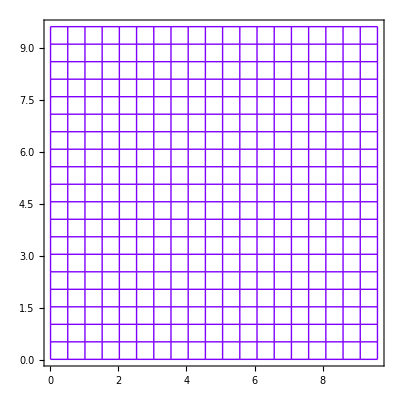

```mathematica
plt[.75,a]
```

```mathematica
r=Exp[I Pi*.25]	(*I=Sqrt[-1]*)
```

0.707107+0.707107 ⅈ

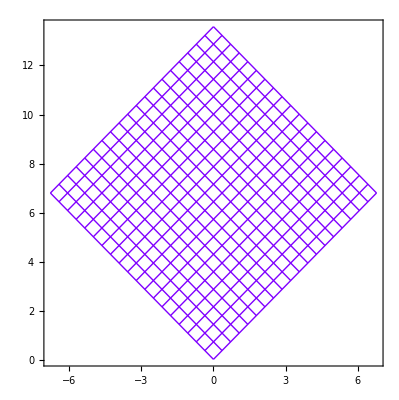

```mathematica
plt[.75,r*a]
(*Rotate of Angle=Pi/4 around zero.r acts to each element of a*)
```

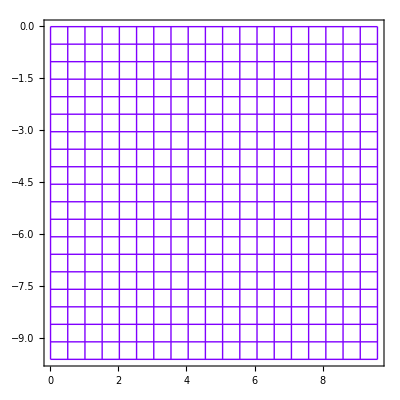

```mathematica
plt[.75,Conjugate[a]]
(*Conjugate acts to each element of a*)
```

## Mapping Lattice

## Function acts to each element of List .

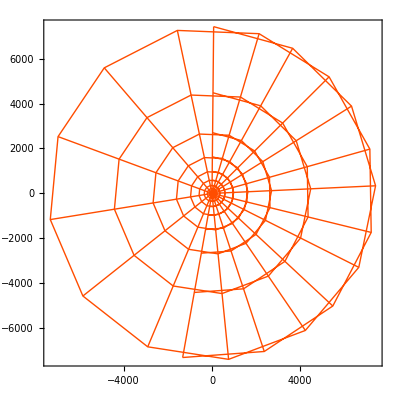

```mathematica
plt[.05,Sin[a]]	(*sine function*)
```

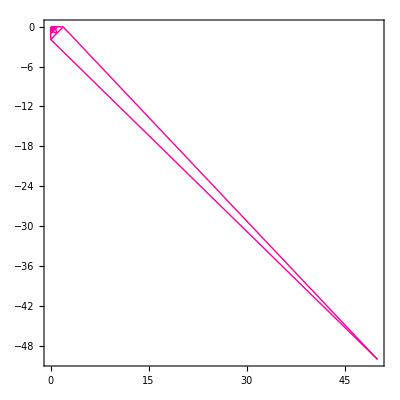

```mathematica
g1=plt[.9,1/a]  (*1/a is inverse of each element of a*)
```

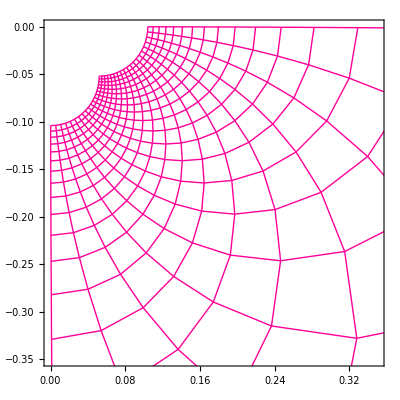

```mathematica
Show[g1,PlotRange->{{0,0.35},{-0.35,0}}]
```

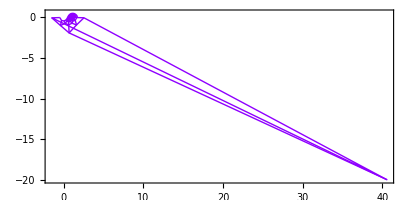

```mathematica
g2=plt[.76,Zeta[a]]	(*Riemann's Zeta function*)
```

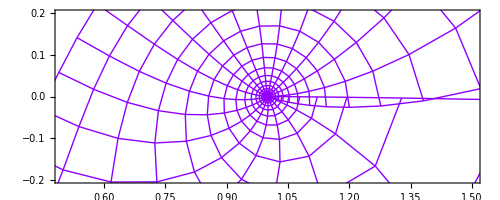

```mathematica
Show[g2,PlotRange->{{0.5,1.5},{-0.2,0.2}}]
```

```mathematica
?BesselJ
```

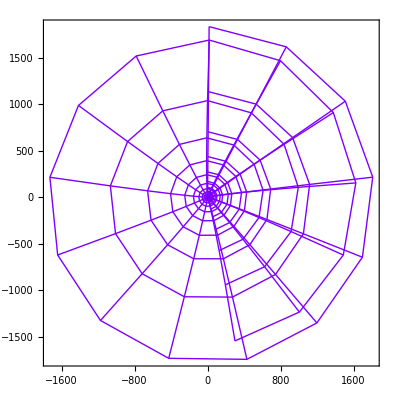

```mathematica
g3=plt[.75,BesselJ[1,a]]
```

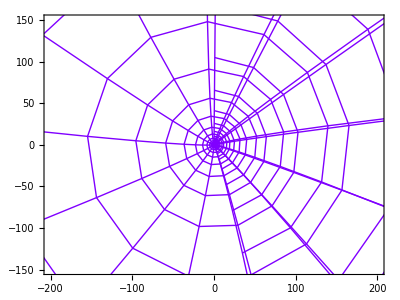

```mathematica
Show[g3,PlotRange->{{-200,200},{-0150,150}}]
```

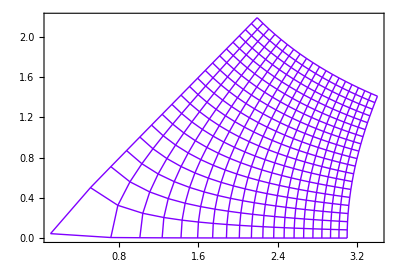

```mathematica
plt[.75,Sqrt[a]]
(*Square Root of each element of a*)
```

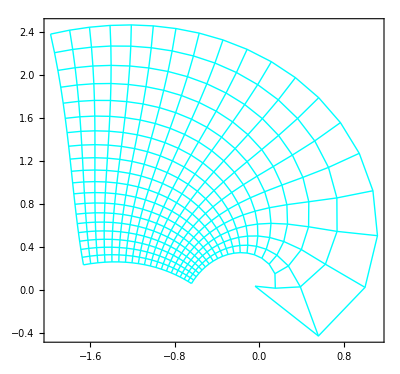

```mathematica
plt[.5,a^(.5+I)]	(*Power by "1/2 + Sqrt[-1]"*)
```

```mathematica
?AiryAi
```

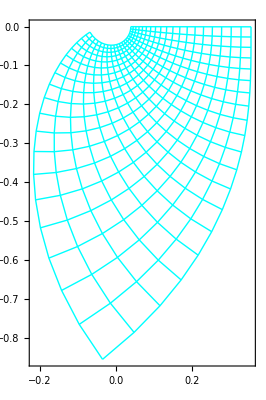

```mathematica
plt[.5,AiryAi[Evaluate[a/5]]]
```

```mathematica
a1=4+4I
```

4+4 ⅈ

```mathematica
a2=6+7I
```

6+7 ⅈ

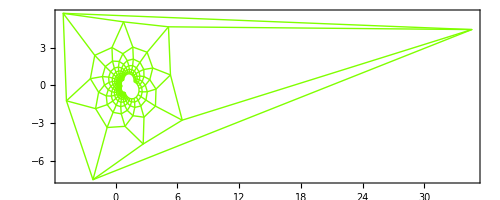

```mathematica
plt[.25,(a-a1)/(a-a2)]
```

## Biblography Programming in Mathematica Second Edition, R . Maeder, Addison - Wesley, 1991